## CEPC CDR inputs dated: Oct.30.2017 by Zhen

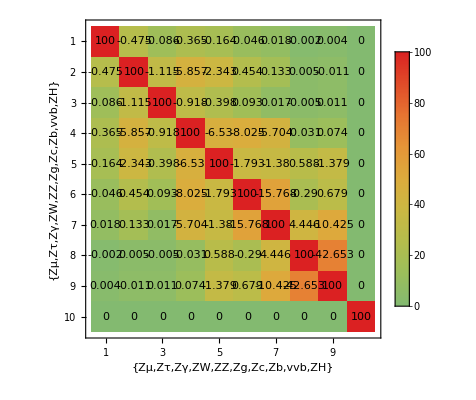

```mathematica
higgsprecepc={15,0.68,8.2,1.2,5.9,1.4,3.5,0.298,3.04,0.50}/100;
inputcorrelations={{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
MatrixPlot[Abs[inputcorrelations],FrameLabel->{{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","vvb","ZH"},{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","vvb","ZH"}},PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[inputcorrelations[[i,j]],{i-0.5,10-j+0.5}],{i,1,10},{j,1,10}]]]
```

## CEPC CDR inputs dated: July.2.2018 by Zhen (based on inputs developed in May)

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc=(*July.20.2018; Note that the second to last entry is infinity to avoid double counting*){16.8,0.87,7.25,1.00,5.21,1.34,3.43,0.324,3.16,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
higgsobscepcinv=0.165/100;
halfcorrelation=(*July.20.2018*)SparseArray[{{11,11}->0,{4,2}->-13.286,{5,2}->-6.669,{6,2}->0.864,{7,2}->0.638,{8,2}->-0.025,{9,2}->-0.011,{10,2}->-0.075,{5,4}->-32.350,{6,4}->-3.644,{7,4}->-2.869,{8,4}->1.140,{9,4}->-0.521,{10,4}->0.328,{6,5}->-1.926,{7,5}->-1.167,{8,5}->-1.809,{9,5}->0.827,{10,5}->0.148,{7,6}->-22.332,{8,6}->-12.429,{9,6}-> 5.681,{10,6}->-1.680,{8,7}-> -7.027,{9,7}-> 3.212,{10,7}-> -6.498,{9,8}-> -45.706,{10,8}-> 0.918,{10,9}-> -0.420}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
MatrixPlot[Abs[inputcorrelations],FrameLabel->{{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","WWbb","vvb","ZH"},{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","WWbb","vvb","ZH"}},PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[SetPrecision[inputcorrelations[[i,j]],3],{i-0.5,11-j+0.5}],{i,1,11},{j,1,11}]]]
```

-Graphics-

```mathematica
Length[inputcorrelations]
```

11

## HL-LHC ECFA updated inputs

For constrained kappa for now

From https://twiki.cern.ch/twiki/bin/view/LHCPhysics/GuidelinesCouplingProjections2018

```mathematica
higgsobslhc7s2[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kgamma,kw,kz,kg,kt,kb,ktau,ktau};
higgsprelhc7s2={2.0,1.8,1.7,2.5,3.5,4.0,2.0,5.0}/100;
halfcorrelationlhc7s2=(*July.20.2018*)SparseArray[{{1,2}->0.66,{1,3}->0.57,{1,4}->0.29,{1,5}->0.18,{1,6}->0.65,{1,7}->0.66,{1,8}->0.27,
{2,3}->0.58,{2,4}->0.39,{2,5}->0.25,{2,6}->0.74,{2,7}->0.59,{2,8}->0.27,
{3,4}->0.24,{3,5}->0.24,{3,6}->0.56,{3,7}->0.50,{3,8}->0.23,
{4,5}->0.34,{4,6}->0.67,{4,7}->0.43,{4,8}->0.09,
{5,6}->0.38,{5,7}->0.26,{5,8}->0.09,
{6,7}->0.70,{6,8}->0.26,
{7,8}->0.25,{8,8}->0}]//Normal;
inputcorrelationslhc7s2=(*Apr.15.2018*)IdentityMatrix[8]*100+halfcorrelationlhc7s2ᵀ*100+halfcorrelationlhc7s2*100;
MatrixPlot[Abs[inputcorrelationslhc7s2],FrameLabel->{{"κγ","κw","κz","κg","κt","κb","κτ","κμ"}},PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[SetPrecision[inputcorrelationslhc7s2[[i,j]],3],{i-0.5,Length[inputcorrelationslhc7s2]-j+0.5}],{i,1,Length[inputcorrelationslhc7s2]},{j,1,Length[inputcorrelationslhc7s2]}]]]
```

-Graphics-